```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ethans/Documents/Courses/MATH161/Notes/6-OneSidedLimits

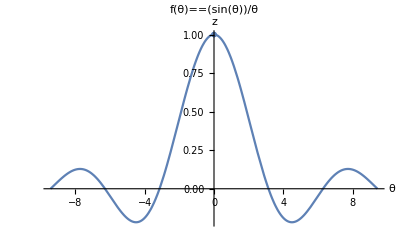

ex5.png

```mathematica
f[θ_]=Sin[θ]/θ;
{a,b}={-3*Pi,3*Pi};
plt=Show[
Plot[f[θ],{θ,a,b},PlotLabel->HoldForm[f[θ]]==f[θ],AxesLabel->{θ,z}],
ListPlot[{{0,1}},PlotMarkers->"OpenMarkers",ImageSize->Large]
]
Export["ex5.png",plt]
```